This is for generating raw images for the Reaching Limits manuscript (C. Richards, T. Murtola, 2024)
Figure files are in ReachingLimitsFigures.ppt

WARNING!  To run this code, change the filename locations below as appropriate

Key data set: setN02_ALLC
see targ_setN02_f.xlsx for explicit conditions fed into the simulator

```mathematica
Qonpc= False;
dirFigures="/Users/chris/Desktop/WTageing/papers/ReachingLimits";
dirFiguresPC="C:\\Users\\ctrichards\\Desktop\\temp_ReachingLimits";
dirMSdata="/Users/chris/Desktop/WTageing/papers/ReachingLimits/data";
dirMSdataPC="C:\\Users\\ctrichards\\Desktop\\temp_ReachingLimits\\data";
dirFigures=If[Qonpc, dirFiguresPC,dirFigures]
dirMSdata=If[Qonpc,dirMSdataPC,dirMSdata]
```

/Users/chris/Desktop/WTageing/papers/ReachingLimits

/Users/chris/Desktop/WTageing/papers/ReachingLimits/data

## !!Please evaluate the relevant sections of analyseReaches.nb prior to running this code!! Submission 2 Figures (Revised; see below for originals)

## Figure 1

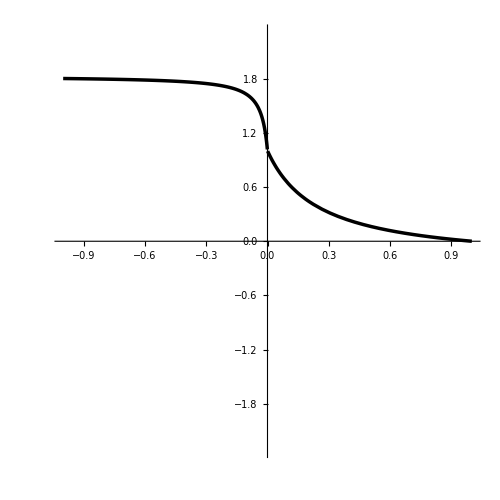

```mathematica
thickness=Thickness[0.005];
styles={{Black,Dashed,thickness},{Gray,thickness},{Gray,Dashed,thickness}};
FVdemo=FVpiecewise[vm,1,fvparam[[1]],fvparam[[2]],fvparam[[3]]];
FVantdemo=FVpiecewise[-vm,1,fvparam[[1]],fvparam[[2]],fvparam[[3]]];



pA=Plot[FVdemo,{vm,-1,1},AspectRatio->1,Ticks->Automatic,LabelStyle->Transparent,BaseStyle->graphstyle,AxesStyle->{{Thin,Black},{Thin,Black}},PlotStyle->{{Black,thickness},{Gray,Dashed,thickness},{Gray,Dashed,thickness}},PlotRange->{{-1,1},{-2.3,2.3}},ImageSize->500]
```

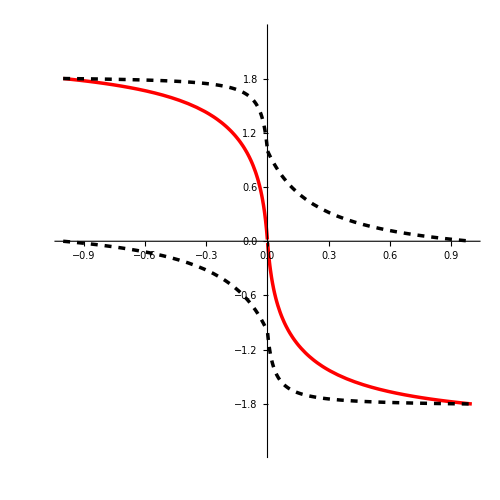

```mathematica
ademo=1;
pB=Plot[{FVdemo-ademo*FVantdemo,FVdemo,-ademo*FVantdemo},{vm,-1,1},AspectRatio->1,Ticks->Automatic,LabelStyle->Transparent,BaseStyle->graphstyle,AxesStyle->{{Thin,Black},{Thin,Black}},PlotStyle->{{Red,thickness},{Black,Dashed,thickness},{Black,Dashed,thickness}},PlotRange->{{-1,1},{-2.3,2.3}},ImageSize->500]
```

```mathematica
aElb
```

0.769231

```mathematica
SetDirectory[dirFigures]
Export["PlainFV_joint.png",pB]
```

/Users/chris/Desktop/WTageing/papers/ReachingLimits

PlainFV_joint.png

## Figure 2

```mathematica
thickness=Thickness[0.005];
styles={{Red,thickness},{Black,Dashed,thickness},{Gray,Dashed,thickness}};
FVdemo=FVpiecewise[vm,1,fvparam[[1]],fvparam[[2]],fvparam[[3]]];
FVantdemo=FVpiecewise[-vm,1,fvparam[[1]],fvparam[[2]],fvparam[[3]]];
maxValues={1.1,0.9};
Manipulate[


actpts={a1,a2};

(*imax=Ordering[actpts,-1][[1]](*Max[actPoints]*);
imin=Ordering[actpts,1][[1]](*Min[actPoints]*);*)
imin=2;imax=1;
ademo=maxValues[[imax]]/maxValues[[imin]];

(*pA=Plot[{FVdemo,FVantdemo,FVdemo-a*FVantdemo},{vm,-1,1},AspectRatio->1,Ticks->Automatic,LabelStyle->Transparent,BaseStyle->graphstyle,AxesStyle->{{Thin,Black},{Thin,Black}},PlotStyle->{{Black,thickness},{Gray,Dashed,thickness},{Gray,Dashed,thickness}},PlotRange->{{-1,1},{-2.3,2.3}},ImageSize->500];*)

pC=Plot[{Max[actpts]*FVdemo-ademo*Min[actpts]*FVantdemo,Max[actpts]*FVdemo,Max[actpts]*FVdemo-ademo*Max[actpts]*FVantdemo},{vm,-1,1},AspectRatio->1,Ticks->Automatic,LabelStyle->Transparent,BaseStyle->graphstyle,AxesStyle->{{Thin,Black},{Thin,Black}},PlotStyle->styles,PlotRange->{{-1,1},{-2.3,2.3}},Filling->{2->{3}},FillingStyle->Setting[0.8800488288700694],ImageSize->500];

plot=Plot[{actpts[[imax]]*FVdemo-ademo*actpts[[imin]]*FVantdemo,actpts[[imax]]*FVdemo,(*actpts[[imax]]*FVdemo*)-ademo*actpts[[imin]]*FVantdemo},{vm,-1,1},AspectRatio->1,Ticks->Automatic,LabelStyle->Transparent,BaseStyle->graphstyle,AxesStyle->{{Thin,Black},{Thin,Black}},PlotStyle->styles,PlotRange->{{-1,1},{-2.3,2.3}},ImageSize->500];

plot
(*pC*)

,{{a1,1(*For C = 0.25*)},0,1},{{a2(*For C = 1*),0.5},0,1}]
```

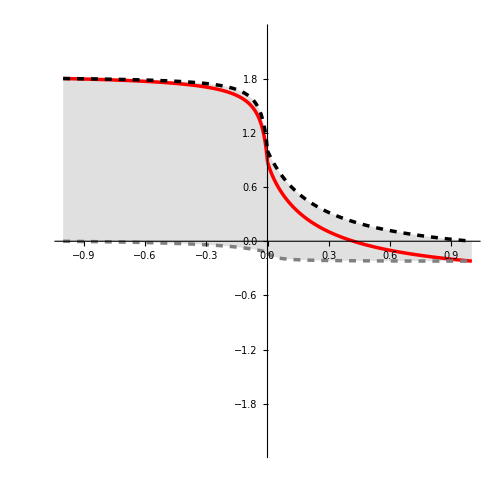

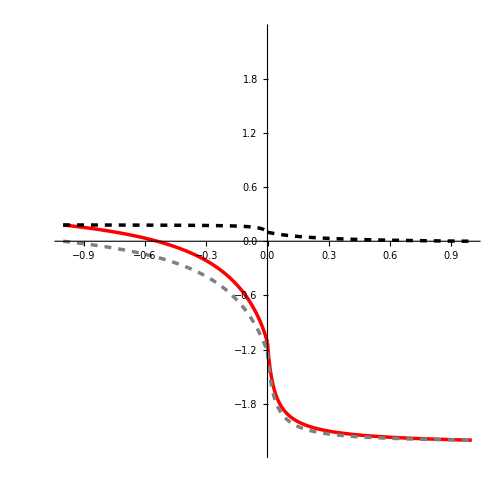

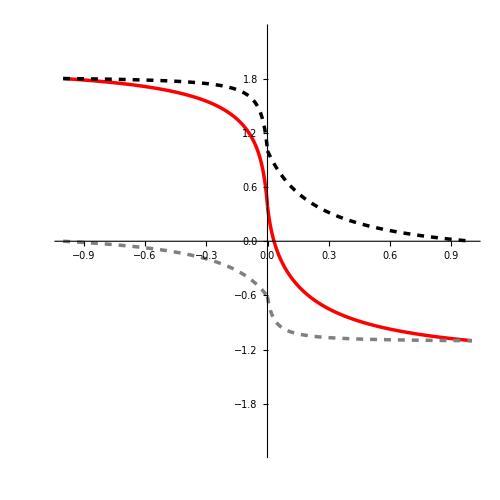

```mathematica
(*note the order is red cuve, top curve, bottom curve*)
agAct=1;antAct=0.1;
pA=Plot[{agAct*FVdemo-ademo*antAct*FVantdemo,agAct*FVdemo,-ademo*antAct*FVantdemo},{vm,-1,1},AspectRatio->1,Ticks->Automatic,LabelStyle->Transparent,BaseStyle->graphstyle,AxesStyle->{{Thin,Black},{Thin,Black}},PlotStyle->styles,PlotRange->{{-1,1},{-2.3,2.3}},ImageSize->500,PlotPoints->500,Filling->{2->{3}},FillingStyle->Setting[0.8800488288700694]]
agAct=0.1;antAct=1;
pB=Plot[{agAct*FVdemo-ademo*antAct*FVantdemo,agAct*FVdemo,-ademo*antAct*FVantdemo},{vm,-1,1},AspectRatio->1,Ticks->Automatic,LabelStyle->Transparent,BaseStyle->graphstyle,AxesStyle->{{Thin,Black},{Thin,Black}},PlotStyle->styles,PlotRange->{{-1,1},{-2.3,2.3}},ImageSize->500,PlotPoints->500,Filling->{2->{3}},FillingStyle->Transparent]
agAct=1;antAct=0.5;
pC=Plot[{agAct*FVdemo-ademo*antAct*FVantdemo,agAct*FVdemo,-ademo*antAct*FVantdemo},{vm,-1,1},AspectRatio->1,Ticks->Automatic,LabelStyle->Transparent,BaseStyle->graphstyle,AxesStyle->{{Thin,Black},{Thin,Black}},PlotStyle->styles,PlotRange->{{-1,1},{-2.3,2.3}},ImageSize->500,PlotPoints->500,Filling->{2->{3}},FillingStyle->Transparent]
```

```mathematica
SetDirectory[dirFigures]
Export["FVplotDemoA.png",pA]
Export["FVplotDemoB.png",pB]
Export["FVplotDemoC.png",pC]
```

/Users/chris/Desktop/WTageing/papers/ReachingLimits

FVplotDemoA.png

FVplotDemoB.png

FVplotDemoC.png

```mathematica
pA
```

## Figure 3

Run initialisation cell for analyseReaches.nb prior to running this cell

```mathematica
(*import hypothetical data for fig 3*)
SetDirectory[dirdata];
exampleDATAraw=Import["FV_example_data.csv","Data"];
firstRow=exampleDATAraw[[1]]
exampleDATA=exampleDATAraw[[2;;]];
examplefvsDATAraw=Import["FV_example_fvs.csv","Data"];
firstRowfvs=examplefvsDATAraw[[1]]
examplefvsDATA=examplefvsDATAraw[[2;;]];

ResetDirectory[];
```

{Norm time,Planned angle,Planned vel,Planned acc,Planned torque,Planned ag act,Planned ant act,PD angle,PD vel,PD acc,PD torque,PD ag act,PD ant act}

{Joint vel,Norm joint vel,Ag FV,Ant FV}

```mathematica
timeData=exampleDATA[[;;,1]];
angTR=exampleDATA[[;;,2]];(*target angle*)
velTR=exampleDATA[[;;,3]];(*target vel*)
accTR=exampleDATA[[;;,4]];(*target acc*)
trqTR=exampleDATA[[;;,5]];(*target torque*)
agoTR=exampleDATA[[;;,6]];(*target agonist activation*)
antTR=exampleDATA[[;;,7]];(*target antagonist activation*)
angPD=exampleDATA[[;;,8]];(*PD controlled angle*)
velPD=exampleDATA[[;;,9]];(*PD controlled vel*)
accPD=exampleDATA[[;;,10]];(*PD controlled accel*)
trqPD=exampleDATA[[;;,11]];(*PD controlled torque*)
agoPD=exampleDATA[[;;,12]];(*PD controlled agonist activation*)
antPD=exampleDATA[[;;,13]];(*PD controlled antagonist activation*)

jvel=examplefvsDATA[[;;,1]];(*joint velocity*)
agofv=examplefvsDATA[[;;,3]];(*agonist fv*)
antfv=examplefvsDATA[[;;,4]];(*antagonist fv*)
```

```mathematica
pA=Show[
ListLinePlot[Thread[{timeData,angTR}],PlotStyle->{Black,Dashed}],
ListLinePlot[Thread[{timeData,angPD}],PlotStyle->{Thick,Blue}]
,PlotRange->All,PlotStyle->styles3,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]
];

pB=Show[
ListLinePlot[Thread[{timeData,velTR}],PlotStyle->{Black,Dashed}],
ListLinePlot[Thread[{timeData,velPD}],PlotStyle->{Thick,Blue}]
,PlotRange->All,PlotStyle->styles3,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]
];

pC=Show[
ListLinePlot[Thread[{timeData,trqTR}],PlotStyle->{Black,Dashed}],
ListLinePlot[Thread[{timeData,trqPD}],PlotStyle->{Thick,Blue}]
,PlotRange->All,PlotStyle->styles3,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]
];

pD=Show[
ListLinePlot[Thread[{timeData,agoTR}],PlotStyle->{Black,Dashed, Thickness[0.008]}],
ListLinePlot[Thread[{timeData,antTR}],PlotStyle->{Black,Dotted}],
ListLinePlot[Thread[{timeData,agoPD}],PlotStyle->{Blue,Dashed, Thick}],
ListLinePlot[Thread[{timeData,antPD}],PlotStyle->{Blue,Dotted}]
,PlotRange->All,PlotStyle->styles3,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]
];

normTime=0.2;
tindex=1000*normTime;
aAGO=agoTR[[tindex]];
aANT=antTR[[tindex]]
pagoCurve=ListLinePlot[Thread[{jvel,aAGO*agofv}],PlotStyle->{Red,Thick}];
pantCurve=ListLinePlot[Thread[{jvel,aANT*antfv}],PlotStyle->{Red,Thick}];
pEggPD=ListLinePlot[Thread[{velPD[[;;tindex]],trqPD[[;;tindex]]}],PlotStyle->{Blue}];
pEggTR=ListLinePlot[Thread[{velTR[[;;tindex]],trqTR[[;;tindex]]}],PlotStyle->{Black,Thick,Dashed},PlotRange->{{-0.2,1.1},{-1,1}},AspectRatio->1,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]];

pE=Show[
pEggTR,
pEggPD,
pagoCurve,
pantCurve
];

normTime=0.6;
tindex=1000*normTime;
aAGO=agoTR[[tindex]];
aANT=antTR[[tindex]]
pagoCurve=ListLinePlot[Thread[{jvel,aAGO*agofv}],PlotStyle->{Red,Thick}];
pantCurve=ListLinePlot[Thread[{jvel,aANT*antfv}],PlotStyle->{Red,Thick}];
pEggPD=ListLinePlot[Thread[{velPD[[;;tindex]],trqPD[[;;tindex]]}],PlotStyle->{Blue}];
pEggTR=ListLinePlot[Thread[{velTR[[;;tindex]],trqTR[[;;tindex]]}],PlotStyle->{Black,Thick,Dashed},PlotRange->{{-0.2,1.1},{-1,1}},AspectRatio->1,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]];

pF=Show[
pEggTR,
pEggPD,
pagoCurve,
pantCurve
];

normTime=1;
tindex=1000*normTime;
aAGO=agoTR[[tindex]];
aANT=antTR[[tindex]]
pagoCurve=ListLinePlot[Thread[{jvel,aAGO*agofv}],PlotStyle->{Red,Thick}];
pantCurve=ListLinePlot[Thread[{jvel,aANT*antfv}],PlotStyle->{Red,Thick}];
pEggPD=ListLinePlot[Thread[{velPD[[;;tindex]],trqPD[[;;tindex]]}],PlotStyle->{Blue}];
pEggTR=ListLinePlot[Thread[{velTR[[;;tindex]],trqTR[[;;tindex]]}],PlotStyle->{Black,Thick,Dashed},PlotRange->{{-0.2,1.1},{-1,1}},AspectRatio->1,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]];

pG=Show[
pEggTR,
pEggPD,
pagoCurve,
pantCurve
];

normTime=1.5;
tindex=1000*normTime;
aAGO=agoTR[[tindex]];
aANT=antTR[[tindex]]
pagoCurve=ListLinePlot[Thread[{jvel,aAGO*agofv}],PlotStyle->{Red,Thick}];
pantCurve=ListLinePlot[Thread[{jvel,aANT*antfv}],PlotStyle->{Red,Thick}];
pEggPD=ListLinePlot[Thread[{velPD[[;;tindex]],trqPD[[;;tindex]]}],PlotStyle->{Blue}];
pEggTR=ListLinePlot[Thread[{velTR[[;;tindex]],trqTR[[;;tindex]]}],PlotStyle->{Black,Thick,Dashed},PlotRange->{{-0.2,1.1},{-1,1}},AspectRatio->1,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]];

pH=Show[
pEggTR,
pEggPD,
pagoCurve,
pantCurve
];
```

0

0.124654

0.00448609

0

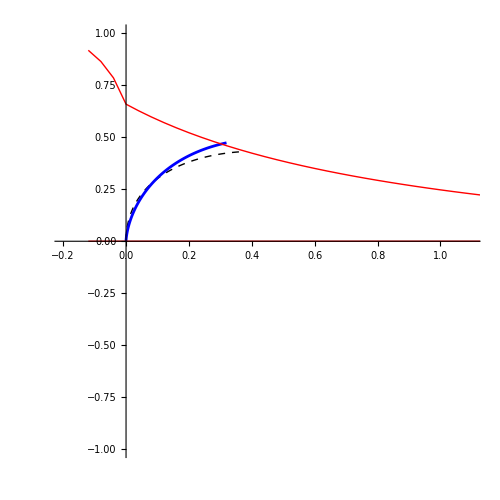

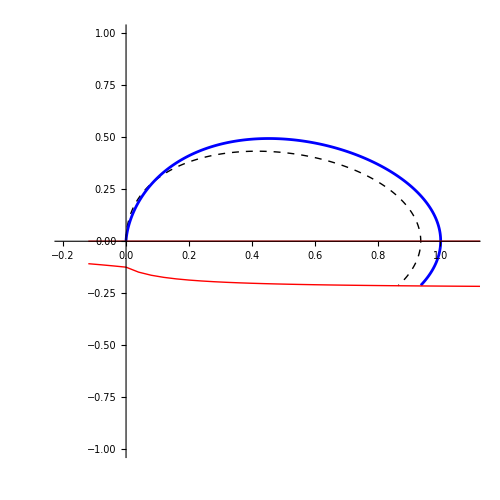

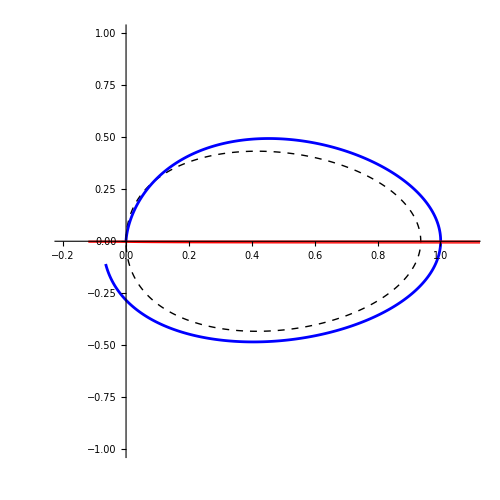

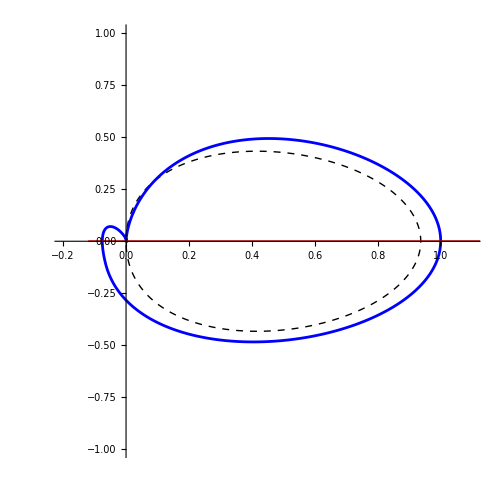

```mathematica
pE
pF
pG
pH
```

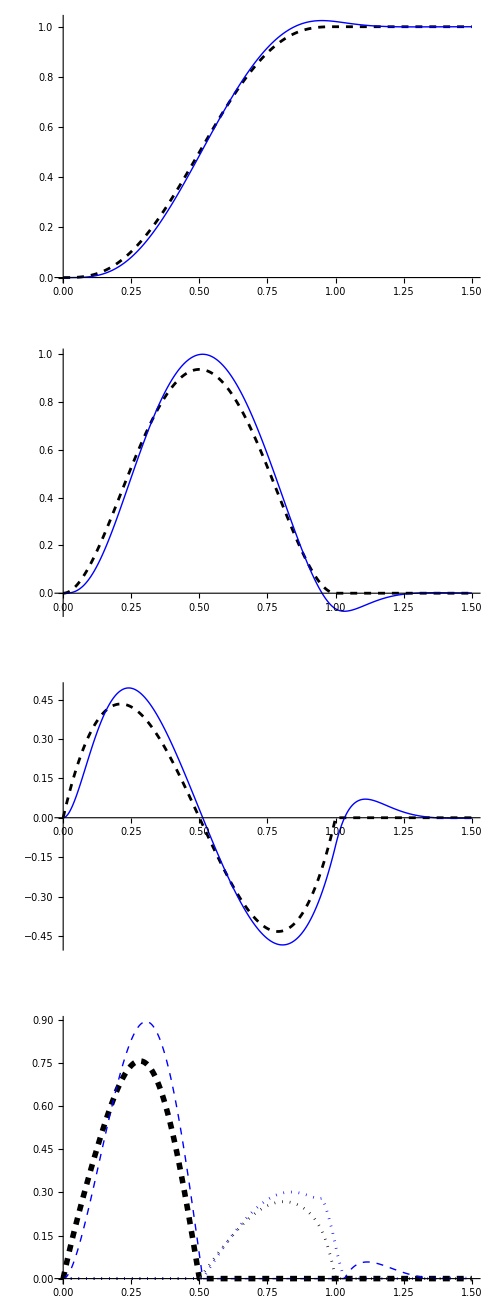

```mathematica
GraphicsColumn[{pA,pB,pC,pD},ImageSize->500]
```

```mathematica
Length[timeData]
```

1501

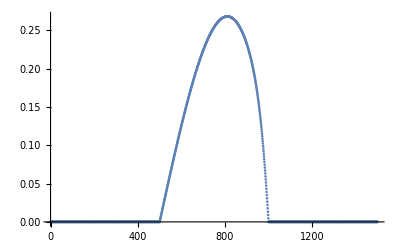

```mathematica
ListPlot[antTR]
```

## Figure 4

Run analyseReaches for the control condition ”A03_FB_P00_f0”

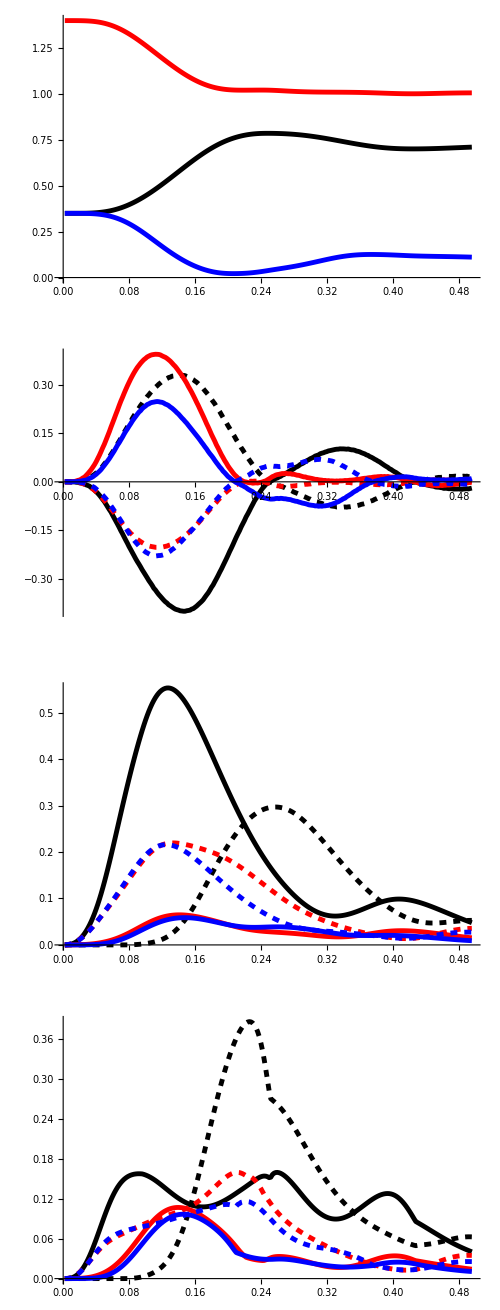

```mathematica
figurePlot=GraphicsColumn[{pang,pvel,pact,pfrc},ImageSize->500,ImagePadding->{{Automatic,Automatic},None}]
```

```mathematica
SetDirectory[dirFigures]
Export["timeSeriesData.png",figurePlot]
```

/Users/chris/Desktop/WTageing/papers/ReachingLimits

timeSeriesData.png

## Figures 5,6,7

Run analyseReaches for the control condition “A03_FB_P00_f0”

```mathematica
qExport=True;
SetDirectory[dirFigures(*dirFiguresPC*)];
yrange=(*0.05*)(*0.75*)0.5;
pertTimings={
{"A03_FB_P01_f0",0.022},{"A03_FB_P02_f0",0.064},{"A03_FB_P03_f0",0.106},{"A03_FB_P04_f0",0.148},
{"A03_FB_P01_f1",0.032},{"A03_FB_P02_f1",0.094},{"A03_FB_P03_f1",0.158},{"A03_FB_P04_f1",0.222},
{"A03_FB_P01_f2",0.038},{"A03_FB_P02_f2",0.116},{"A03_FB_P03_f2",0.192},{"A03_FB_P04_f2",0.270}
};
(*perturbation never happens for controls, so make start time arbitrarily large*)
pertTimingsControl={{"A03_FB_P00_f0",10},{"A03_FB_P00_f1",10},{"A03_FB_P00_f2",10}};
pertTimings=Join[pertTimings,pertTimingsControl];
pertStart=pertTimings[[Position[pertTimings,trialname][[1,1]]]][[2]];
pertEnd=pertStart+0.018;

range=1;
ptarget=ListPointPlot3D[{targetXYZ},PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1},PlotStyle->Red,Axes->False,Boxed->False];
(*reachAnim=Table*)
frames={25,50,100,150,200,225};
joint=1;
framePanels=Do[
fr=frames[[i]];
time=ToString[NumberForm[fr*mjdt,{3,3}]]<>"s";
labelnormal=Style[time,Black,Bold,20];
labelperturb=Style[time,Red,Bold,20];
label=If[pertStart<=fr*mjdt<=pertEnd,labelperturb,labelnormal];
points=Partition[xyzDATA[[fr]],3];
DATA={shofvDATA2D,elbfvDATA2D,wrifvDATA2D}[[joint]];
p2=Graphics3D[{Thickness[0.007],Line[points]}];
plot1=Show[ptarget,p2,Box->False,ViewPoint->Top,ViewAngle->0.4];
plot2=Show[
DATA[[fr]],
PlotRange->{All,{-yrange,yrange}},PlotStyle->Thick,(*PlotLabel->label,*)BaseStyle->graphstyle,AxesStyle->Thickness[axthickness]];
(*GraphicsRow[{plot1,plot2},ImageSize->800]*)
frame=Show[plot2,Epilog->Inset[label,Scaled[{0.15,.95}]],ImageSize->500];
frameSho=frame;
(*frame=Show[plot2,ImageSize->500];*)
framesho=frame;
If[qExport,
Export["shoFVframe"<>IntegerString[i,10,2]<>".png",frame];
];
,{i,1,Length[frames]}];

joint=2;
framePanels=Do[
fr=frames[[i]];
time=ToString[NumberForm[fr*mjdt,{3,3}]]<>"s";
labelnormal=Style[time,Black,Bold,20];
labelperturb=Style[time,Red,Bold,20];
label=If[pertStart<=fr*mjdt<=pertEnd,labelperturb,labelnormal];
points=Partition[xyzDATA[[fr]],3];
DATA={shofvDATA2D,elbfvDATA2D,wrifvDATA2D}[[joint]];
p2=Graphics3D[{Thickness[0.007],Line[points]}];
plot1=Show[ptarget,p2,Box->False,ViewPoint->Top,ViewAngle->0.4];
plot2=Show[
DATA[[fr]],
PlotRange->{All,{-yrange,yrange}},PlotStyle->Thick,(*PlotLabel->label,*)BaseStyle->graphstyle,AxesStyle->Thickness[axthickness]];
(*GraphicsRow[{plot1,plot2},ImageSize->800]*)
frame=Show[plot2,Epilog->Inset[label,Scaled[{0.15,.95}]],ImageSize->500];
(*frame=Show[plot2,ImageSize->500];*)
frameelb=frame;
If[qExport,
Export["elbFVframe"<>IntegerString[i,10,2]<>".png",frame];
];
,{i,1,Length[frames]}];

joint=3;
framePanels=Do[
fr=frames[[i]];
time=ToString[NumberForm[fr*mjdt,{3,3}]]<>"s";
labelnormal=Style[time,Black,Bold,20];
labelperturb=Style[time,Red,Bold,20];
label=If[pertStart<=fr*mjdt<=pertEnd,labelperturb,labelnormal];
points=Partition[xyzDATA[[fr]],3];
DATA={shofvDATA2D,elbfvDATA2D,wrifvDATA2D}[[joint]];
p2=Graphics3D[{Thickness[0.007],Line[points]}];
plot1=Show[ptarget,p2,Box->False,ViewPoint->Top,ViewAngle->0.4];
plot2=Show[
DATA[[fr]],
PlotRange->{All,{-yrange,yrange}},PlotStyle->Thick,(*PlotLabel->label,*)BaseStyle->graphstyle,AxesStyle->Thickness[axthickness]];
(*GraphicsRow[{plot1,plot2},ImageSize->800]*)
frame=Show[plot2,Epilog->Inset[label,Scaled[{0.15,.95}]],ImageSize->500];
(*frame=Show[plot2,ImageSize->500];*)
framewri=frame;
If[qExport,
Export["wriFVframe"<>IntegerString[i,10,2]<>".png",frame];
];
,{i,1,Length[frames]}];


framePanelsStick=Do[
fr=frames[[i]];
time=ToString[NumberForm[fr*mjdt,{3,3}]]<>"s";
labelnormal=Style[time,Black,Bold,20];
labelperturb=Style[time,Red,Bold,20];
label=If[pertStart<=fr*mjdt<=pertEnd,labelperturb,labelnormal];
points=Partition[xyzDATA[[fr]],3];
DATA={shofvDATA2D,elbfvDATA2D,wrifvDATA2D}[[joint]];
p2=Graphics3D[{Thickness[0.007],Line[points]}];
plot1=Show[ptarget,p2,Box->False,ViewPoint->Top,ViewAngle->0.4];
plot2=Show[
DATA[[fr]],
PlotRange->{All,{-yrange,yrange}},PlotStyle->Thick,PlotLabel->label];
(*GraphicsRow[{plot1,plot2},ImageSize->800]*)
frame=Show[plot1,ImageSize->500];
If[qExport,
Export["shoStickframe"<>IntegerString[i,10,2]<>".png",frame];
];
,{i,1,Length[frames]}];
```

## Figure 8

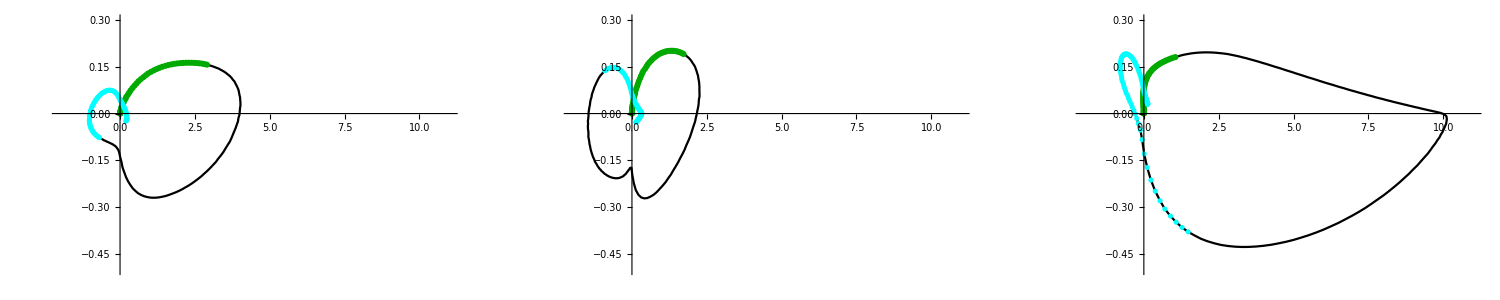

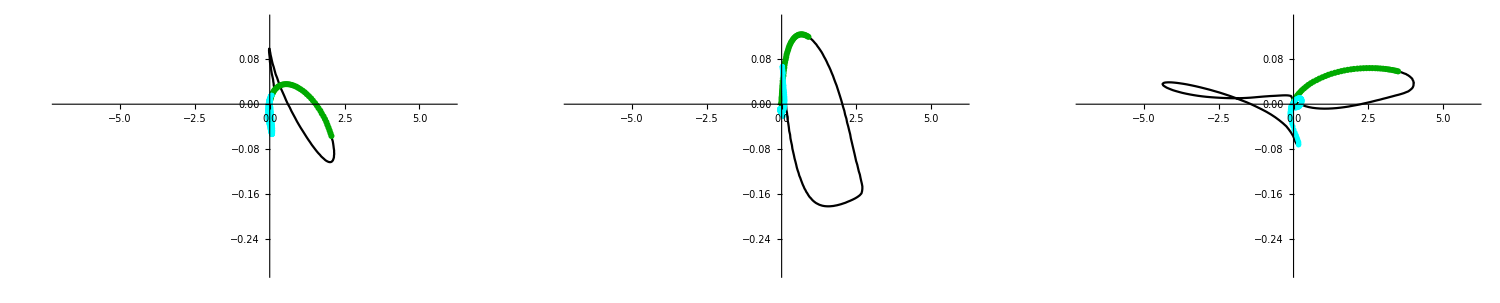

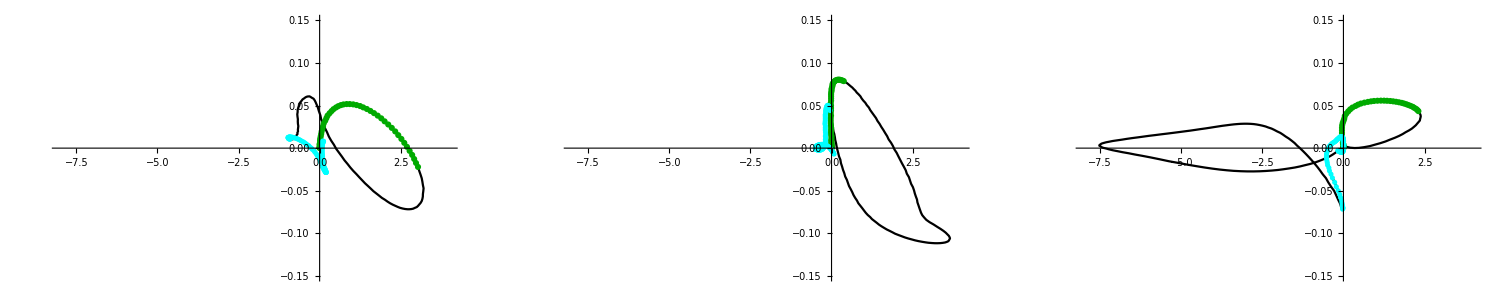

```mathematica
(*open saved data from different reaches*)
mjdt=0.002;(*timestep set in MuJoCo simulation*)
SetDirectory[dirMSdata];
trialroot="A03_FB_P00_f";
reaches={"0","1","2"};(*reach trials*)
joints={"sho","elb","wri"};
trialroot="fvposDATA_A03_FB_P00_f";
reaches={"0","1","2"};(*reach trials*)
joints={"sho","elb","wri"};
suffix=".csv";
msDATAraw=Table[
trname=joints[[i]]<>trialroot<>reaches[[k]]<>suffix;
Import[trname,"Data"]
,{i,1,3},{k,1,3}];

ResetDirectory[];

shoxyrange={{-2,11},{-0.5,0.3}};
elbxyrange={{-7,6},{-0.3,0.15}};
wrixyrange={{-8,4},{-0.15,0.15}};

shofvDATAalltrials=msDATAraw[[1]];
elbfvDATAalltrials=msDATAraw[[2]];
wrifvDATAalltrials=msDATAraw[[3]];


earlyrange=Round[0.1/mjdt];
laterange=Round[0.2/mjdt];
thicknessf7=Thickness[0.004];
sizef7=1500;
colstart=Darker@Green;
colend=Cyan;
GraphicsRow[
Table[Show[
ListLinePlot[shofvDATAalltrials[[i]],PlotRange->shoxyrange,PlotStyle->{Black,thicknessf7},BaseStyle->graphstyle,AxesStyle->Thickness[axthickness]](*whole trial*),
ListPlot[shofvDATAalltrials[[i,1;;earlyrange]],PlotRange->shoxyrange,PlotStyle->colstart](*early portion*),
ListPlot[shofvDATAalltrials[[i,-laterange;;]],PlotRange->shoxyrange,PlotStyle->colend](*lateportion*)
(*,ImageSize->size*)]
,{i,1,3}]
,ImageSize->sizef7]

GraphicsRow[
Table[Show[
ListLinePlot[elbfvDATAalltrials[[i]],PlotRange->elbxyrange,PlotStyle->{Black,thicknessf7},BaseStyle->graphstyle,AxesStyle->Thickness[axthickness]](*whole trial*),
ListPlot[elbfvDATAalltrials[[i,1;;earlyrange]],PlotStyle->colstart](*early portion*),
ListPlot[elbfvDATAalltrials[[i,-laterange;;]],PlotStyle->colend](*lateportion*)
(*,ImageSize->size*)]
,{i,1,3}]
,ImageSize->sizef7]

GraphicsRow[
Table[Show[
ListLinePlot[wrifvDATAalltrials[[i]],PlotRange->wrixyrange,PlotStyle->{Black,thicknessf7},BaseStyle->graphstyle,AxesStyle->Thickness[axthickness]](*whole trial*),
ListPlot[wrifvDATAalltrials[[i,1;;earlyrange]],PlotStyle->colstart](*early portion*),
ListPlot[wrifvDATAalltrials[[i,-laterange;;]],PlotStyle->colend](*lateportion*)
(*,ImageSize->size*)]
,{i,1,3}]
,ImageSize->sizef7]
```

```mathematica
(*for the stick figures*)

SetDirectory[dirFigures];
range=1;
ptarget=ListPointPlot3D[{targetXYZ},PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1},PlotStyle->{Red,PointSize[0.04]},Axes->False,Boxed->False];
stickframes={1,100,-1};
Do[
points=Partition[xyzDATA[[stickframes[[fr]]]],3];
p2=Graphics3D[{Thickness[0.007],Line[points]}];
plot1=Show[ptarget,p2,Box->False,ViewPoint->Top,ViewAngle->0.4];
Export["stickFrames_"<>IntegerString[fr,10,2]<>"_"<>trialname<>".png",plot1]
,{fr,1,Length[stickframes]}]

ResetDirectory[];
```

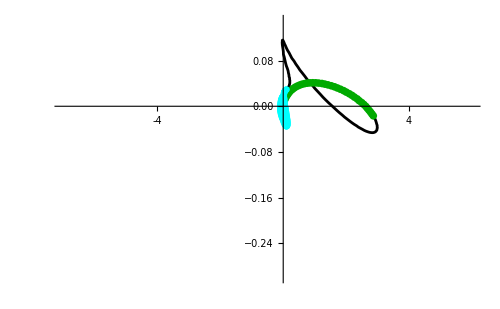

```mathematica
Show[
ListLinePlot[elbfvDATAalltrials[[1]],PlotRange->elbxyrange,PlotStyle->{Black,thicknessf7},BaseStyle->graphstyle,AxesStyle->Thickness[axthickness]](*whole trial*),
ListPlot[elbfvDATAalltrials[[1,1;;earlyrange]],PlotStyle->colstart](*early portion*),
ListPlot[elbfvDATAalltrials[[1,-laterange;;]],PlotStyle->colend](*lateportion*)
,ImageSize->size,Ticks->{{-4,4},Automatic}]
```

```mathematica
ptarget
```

-Graphics3D-

```mathematica
msDATAraw//Dimensions
```

## Figure 9

Step 1. Run analyseReaches for the control condition “A03_FB_P00_f0”
find the section of code that says in comments “analyse components of dtorque/dt” - set joint index to 2 (for elbow)- run that
Export the figure from this notebook
Step 2. Run analyseReaches for the perturbation condition “A03_FB _P04 _f0”
find the section of code that says in comments “analyse components of dtorque/dt” - set joint index to 2 (for elbow)- run that
Export the figure from this notebook

493.558

760.468

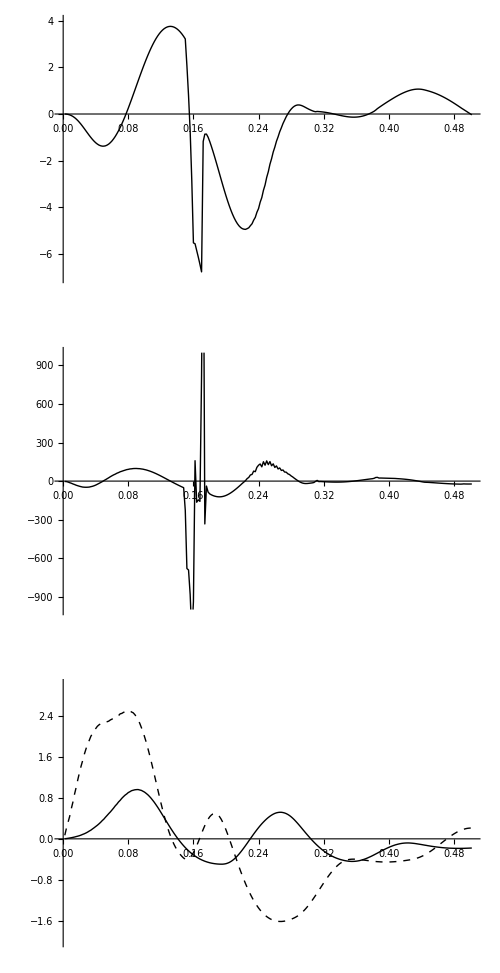

```mathematica
poslimit=Max[Abs@dtorqueLimitPos]
neglimit=Max[Abs@dtorqueLimitNeg]
thickness=Thickness[0.008];
dtorquerange={-1000,1000};

dactJoint=rext*fmaxExt*dadataExt-rflx*fmaxFlx*dadataFlx;
dactFlx=(*rflx*fmaxFlx**)dadataFlx;
dactExt=(*rext*fmaxExt**)dadataExt;
dactJointXY=Thread[{timeData,dactJoint}];
dactFlxXY=Thread[{timeData,(*-*)(*dactFlx*)dadataFlx}];
dactExtXY=Thread[{timeData,(*dactExt*)dadataExt}];

plot1=ListLinePlot[torqueXY,PlotRange->{Automatic,{-7,4}},ImageSize->size,PlotStyle->{Black,Thick},BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]];
plot2=ListLinePlot[{dactExtXY,dactFlxXY},PlotRange->{Automatic,dtorquerange},ImageSize->size,PlotStyle->{{Red,Thick},{Red,Thick,Dashed}},BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]];
plot3=ListLinePlot[dtorqueXY,PlotRange->{Automatic,dtorquerange},ImageSize->size,PlotStyle->{{Black,Thick},{Red,Thick},{Red,Thick,Dashed}},BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]];
plot4=Show[
p1=ListLinePlot[{(*dtorqueXY,dtorqueCalXY,*)dtorqueCalNoACTXY(*dtorqueCalNoFVGXY*)(*,dtorqueCalNoACTXY*)},PlotStyle->{{Blue,thickness},Transparent,{Cyan,Thick},{Blue,Dashed}},PlotRange->{Automatic,dtorquerange},PlotStyle->styles3,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]],
p1a=ListLinePlot[{{0,poslimit},{cutoff,dtorqueLimitPos[[1]]}},PlotStyle->{Black,Dashed}],
p1b=ListLinePlot[{{0,Sign[dtorqueLimitNeg[[1]]]*neglimit},{cutoff,dtorqueLimitPos[[2]]}},PlotStyle->{Black,Dashed}]
];

plot5=ListLinePlot[{dactFlxXY,dactExtXY},PlotRange->{Automatic,{-2,3}},ImageSize->size,PlotStyle->{{Black,Thick},{Black,Thick,Dashed}},BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]];

g=GraphicsColumn[{plot1,plot3,(*plot4,*)(*plot2*)plot5},ImageSize->500]
```

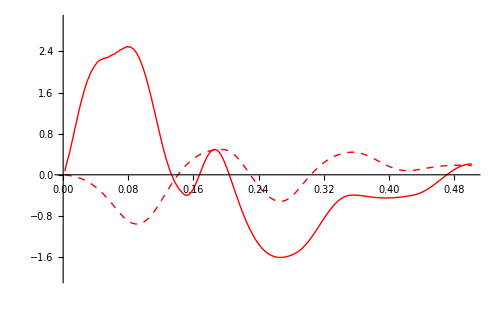

```mathematica
plot5
plot3
```

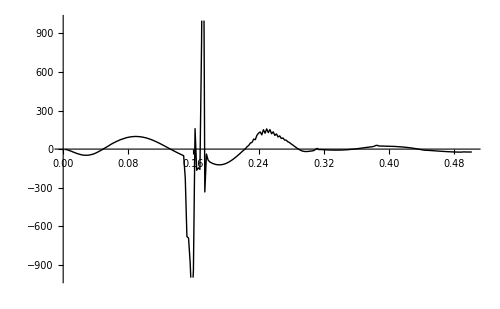

```mathematica
SetDirectory[dirFigures];
Export["C:\\Users\\ctrichards\\Desktop\\"<>"perturbB.png"(*"controlA.png"*),g]
ResetDirectory[];
```

SetDirectory::cdir: Cannot set current directory to /Users/chris/Desktop/WTageing/papers/ReachingLimits.

C:\Users\ctrichards\Desktop\perturbB.png

ResetDirectory::dtop: Directory stack is empty.

```mathematica
aElb
```

1.3

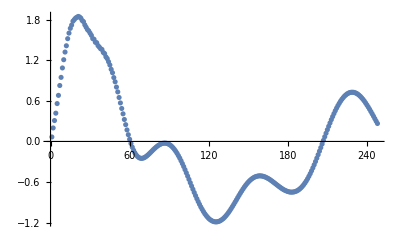

```mathematica
ListPlot[dadataExt-aElb*dadataFlx]
```

## Figure 10

load condition A03_FB _P04 _f0 in analyseReaches.nb

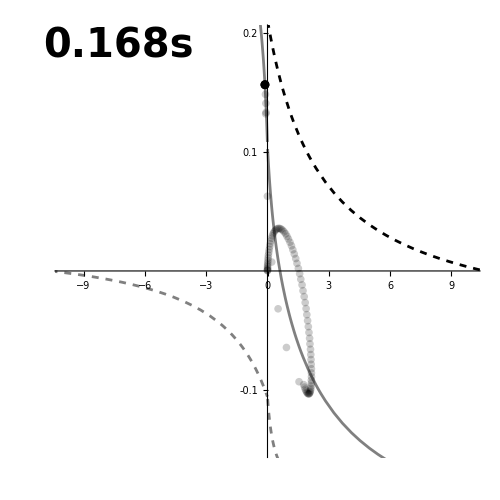

```mathematica
fr=84;(*just after perturbation*)
joint=2;(*elbow joint*)
time=ToString[NumberForm[fr*mjdt,{3,3}]]<>"s";
labelnormal=Style[time,Black,Bold,40];
labelperturb=Style[time,Red,Bold,40];
label=If[pertStart<=fr*mjdt<=pertEnd,labelperturb,labelnormal];
points=Partition[xyzDATA[[fr]],3];
DATA={shofvDATA2D,elbfvDATA2D,wrifvDATA2D}[[joint]];
p2=Graphics3D[{Thickness[0.007],Line[points]}];
plot2=Show[
DATA[[fr]],
PlotRange->(*{All,{-yrange,yrange}}*){{-10,10},{-0.15,0.2}},PlotStyle->Thick,BaseStyle->graphstyle,AxesStyle->Thickness[2*axthickness],Method->{"AxesInFront"->False}];
(*GraphicsRow[{plot1,plot2},ImageSize->800]*)
frame=Show[plot2,Epilog->Inset[label,Scaled[{0.15,.95}]],ImageSize->500,Ticks->{Automatic,{-0.1,0.1,0.2}}]
```

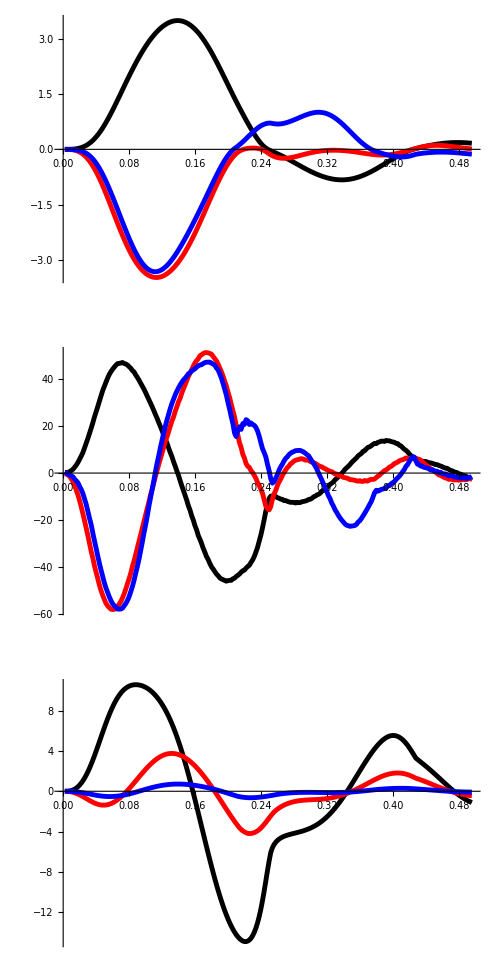

```mathematica
figurePlot=GraphicsColumn[{pqvel,pqacc,ptrq},ImageSize->500,ImagePadding->{{0,Automatic},None}]
```

```mathematica
SetDirectory[dirFigures]
Export["timeSeriesData_torqueandAccel.png",figurePlot]
```

/Users/chris/Desktop/WTageing/papers/ReachingLimits

timeSeriesData_torqueandAccel.png

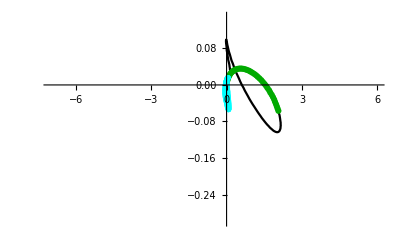

```mathematica
(*open saved data from different reaches*)
SetDirectory[dirMSdata];
trialroot="A03_FB_P00_f";
reaches={"0","1","2"};(*reach trials*)
joints={"sho","elb","wri"};
trialroot="fvposDATA_A03_FB_P00_f";
reaches={"0","1","2"};(*reach trials*)
joints={"sho","elb","wri"};
suffix=".csv";
msDATAraw=Table[
trname=joints[[i]]<>trialroot<>reaches[[k]]<>suffix;
Import[trname,"Data"]
,{i,1,3},{k,1,3}];

ResetDirectory[];

shoxyrange={{-2,11},{-0.5,0.3}};
elbxyrange={{-7,6},{-0.3,0.15}};
wrixyrange={{-8,4},{-0.15,0.15}};

shofvDATAalltrials=msDATAraw[[1]];
elbfvDATAalltrials=msDATAraw[[2]];
wrifvDATAalltrials=msDATAraw[[3]];


earlyrange=Round[0.1/mjdt];
laterange=Round[0.2/mjdt];
thicknessf7=Thickness[0.004];
sizef7=1500;
colstart=Darker@Green;
colend=Cyan;
(*GraphicsRow[
Table[Show[
ListLinePlot[shofvDATAalltrials[[i]],PlotRange->shoxyrange,PlotStyle->{Black,thicknessf7},BaseStyle->graphstyle,AxesStyle->Thickness[axthickness]](*whole trial*),
ListPlot[shofvDATAalltrials[[i,1;;earlyrange]],PlotRange->shoxyrange,PlotStyle->colstart](*early portion*),
ListPlot[shofvDATAalltrials[[i,-laterange;;]],PlotRange->shoxyrange,PlotStyle->colend](*lateportion*)
(*,ImageSize->size*)]
,{i,1,3}]
,ImageSize->sizef7]*)

GraphicsRow[
Table[Show[
ListLinePlot[elbfvDATAalltrials[[i]],PlotRange->elbxyrange,PlotStyle->{Black,thicknessf7},BaseStyle->graphstyle,AxesStyle->Thickness[axthickness],Method->{"AxesInFront"->False}](*whole trial*),
ListPlot[elbfvDATAalltrials[[i,1;;earlyrange]],PlotStyle->colstart,Axes->False](*early portion*),
ListPlot[elbfvDATAalltrials[[i,-laterange;;]],PlotStyle->colend,Axes->False](*lateportion*)
(*,ImageSize->size*)]
,(*{i,1,3}*){i,1,1}]
,ImageSize->sizef7]

(*GraphicsRow[
Table[Show[
ListLinePlot[wrifvDATAalltrials[[i]],PlotRange->wrixyrange,PlotStyle->{Black,thicknessf7},BaseStyle->graphstyle,AxesStyle->Thickness[axthickness]](*whole trial*),
ListPlot[wrifvDATAalltrials[[i,1;;earlyrange]],PlotStyle->colstart](*early portion*),
ListPlot[wrifvDATAalltrials[[i,-laterange;;]],PlotStyle->colend](*lateportion*)
(*,ImageSize->size*)]
,{i,1,3}]
,ImageSize->sizef7]*)
```

## SI movies

movie 3 control reach 1: forward reach (technical name A03_FB_P00_f0)
movie 4 control reach 2: sideways reach (technical name A03_FB_P00_f1)
movie 5 control reach 3: cross-body reach (technical name A03_FB_P00_f2)

movie 6 perturbed reach 1: forward reach (technical name A03_FB_P04_f0)


Directions - run analyseReaches.nb using technical name as the trial name;  run the joint FV volume section

```mathematica
yrange=(*0.05*)(*0.75*)0.5;
pertTimings={
{"A03_FB_P01_f0",0.022},{"A03_FB_P02_f0",0.064},{"A03_FB_P03_f0",0.106},{"A03_FB_P04_f0",0.148},
{"A03_FB_P01_f1",0.032},{"A03_FB_P02_f1",0.094},{"A03_FB_P03_f1",0.158},{"A03_FB_P04_f1",0.222},
{"A03_FB_P01_f2",0.038},{"A03_FB_P02_f2",0.116},{"A03_FB_P03_f2",0.192},{"A03_FB_P04_f2",0.270}
};
(*perturbation never happens for controls, so make start time arbitrarily large*)
pertTimingsControl={{"A03_FB_P00_f0",10},{"A03_FB_P00_f1",10},{"A03_FB_P00_f2",10}};
pertTimings=Join[pertTimings,pertTimingsControl];
pertStart=pertTimings[[Position[pertTimings,trialname][[1,1]]]][[2]];
pertEnd=pertStart+0.018;

isPerturb=ToExpression@StringPart[trialname,10]!=0;(*determine if a perturbed trial*)
pertColor=If[isPerturb,Red,Black];
framePanels={};
ptarget=ListPointPlot3D[{targetXYZ},PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1},PlotStyle->Red,Axes->False,Boxed->False];

(*for stick figure inset*)
framePanelsStick=Table[
fr=i;
time=ToString[NumberForm[fr*mjdt,{3,3}]]<>"s";
labelnormal=Style[time,Black,Bold,20];
labelperturb=Style[time,Red,Bold,20];
label=If[pertStart<=fr*mjdt<=pertEnd,labelperturb,labelnormal];
points=Partition[xyzDATA[[fr]],3];
DATA={shofvDATA2D,elbfvDATA2D,wrifvDATA2D}[[1]];
p2=Graphics3D[{Thickness[0.007],Line[points]}];
plot1=Show[ptarget,p2,Box->False,ViewPoint->Top,ViewAngle->0.4];
plot2=Show[
DATA[[fr]],
PlotRange->{All,{-yrange,yrange}},PlotStyle->Thick,PlotLabel->label];
(*GraphicsRow[{plot1,plot2},ImageSize->800]*)
frame=Show[plot1,ImageSize->500]

,{i,1,Length[actDATA]}];
```

```mathematica
(*for FV trajectories*)
framePanels=Table[
fr=i;
time=ToString[NumberForm[fr*mjdt,{3,3}]]<>"s";

(*time and joint labels*)
sholabelnormal=Style["Shoulder "<>time,Black,Bold,20];
sholabelperturb=Style["Shoulder "<>time,pertColor,Bold,20];
sholabel=If[pertStart<=fr*mjdt<=pertEnd,sholabelperturb,sholabelnormal];

elblabelnormal=Style["Elbow "<>time,Black,Bold,20];
elblabelperturb=Style["Elbow "<>time,pertColor,Bold,20];
elblabel=If[pertStart<=fr*mjdt<=pertEnd,elblabelperturb,elblabelnormal];

wrilabelnormal=Style["Wrist "<>time,Black,Bold,20];
wrilabelperturb=Style["Wrist "<>time,pertColor,Bold,20];
wrilabel=If[pertStart<=fr*mjdt<=pertEnd,wrilabelperturb,wrilabelnormal];

points=Partition[xyzDATA[[fr]],3];
p2=Graphics3D[{Thickness[0.007],Line[points]}];
plot1=Show[ptarget,p2,Box->False,ViewPoint->Top,ViewAngle->0.4];
plotSho=Show[
shofvDATA2D[[fr]],
PlotRange->{All,{-yrange,yrange}},PlotStyle->Thick,PlotLabel->sholabel,BaseStyle->graphstyle,AxesStyle->Thickness[axthickness]];

plotElb=Show[
elbfvDATA2D[[fr]],
PlotRange->{All,{-yrange,yrange}},PlotStyle->Thick,PlotLabel->elblabel,BaseStyle->graphstyle,AxesStyle->Thickness[axthickness]];

plotWri=Show[
wrifvDATA2D[[fr]],
PlotRange->{All,{-yrange,yrange}},PlotStyle->Thick,PlotLabel->wrilabel,BaseStyle->graphstyle,AxesStyle->Thickness[axthickness]];

frameSho=Show[plotSho,ImageSize->500,Epilog->{Inset[framePanelsStick[[fr]],{1,.25},{0,0.5},Scaled[.5]]}];
frameElb=Show[plotElb,ImageSize->500];
frameWri=Show[plotWri,ImageSize->500];

frame=GraphicsRow[{frameSho,frameElb,frameWri},ImageSize->1500]

,{i,1,Length[actDATA]}];

Beep[]
```

```mathematica
SetDirectory[dirFigures];
(*Export["SI_movie_03_control_forward_reach.mov",framePanels]*)
(*Export["SI_movie_04_control_sideways_reach.mov",framePanels]*)
Export["SI_movie_05_control_crossbody_reach.mov",framePanels]
(*Export["SI_movie_06_perturbed_forward_reach.mov",framePanels]*)
Beep[]
ResetDirectory[];
```

SI_movie_05_control_crossbody_reach.mov

# Submission 1 (Original figures)

## Figure 1

```mathematica
thickness=Thickness[0.005];
styles={{Black,Dashed,thickness},{Gray,thickness},{Gray,Dashed,thickness}};
FVdemo=FVpiecewise[vm,1,fvparam[[1]],fvparam[[2]],fvparam[[3]]];
FVantdemo=FVpiecewise[-vm,1,fvparam[[1]],fvparam[[2]],fvparam[[3]]];



pA=Plot[FVdemo,{vm,-1,1},AspectRatio->1,Ticks->Automatic,LabelStyle->Transparent,BaseStyle->graphstyle,AxesStyle->{{Thin,Black},{Thin,Black}},PlotStyle->{{Black,thickness},{Gray,Dashed,thickness},{Gray,Dashed,thickness}},PlotRange->{{-1,1},{-2.3,2.3}},ImageSize->500]
```

-Graphics-

```mathematica
ademo=1;
pB=Plot[{FVdemo-ademo*FVantdemo,FVdemo,-ademo*FVantdemo},{vm,-1,1},AspectRatio->1,Ticks->Automatic,LabelStyle->Transparent,BaseStyle->graphstyle,AxesStyle->{{Thin,Black},{Thin,Black}},PlotStyle->{{Red,thickness},{Black,Dashed,thickness},{Black,Dashed,thickness}},PlotRange->{{-1,1},{-2.3,2.3}},ImageSize->500]
```

-Graphics-

```mathematica
aElb
```

0.769231

```mathematica
SetDirectory[dirFigures]
Export["PlainFV_joint.png",pB]
```

/Users/chris/Desktop/WTageing/papers/ReachingLimits

PlainFV_joint.png

## Figure 2

```mathematica
thickness=Thickness[0.005];
styles={{Red,thickness},{Black,Dashed,thickness},{Gray,Dashed,thickness}};
FVdemo=FVpiecewise[vm,1,fvparam[[1]],fvparam[[2]],fvparam[[3]]];
FVantdemo=FVpiecewise[-vm,1,fvparam[[1]],fvparam[[2]],fvparam[[3]]];
maxValues={1.1,0.9};
Manipulate[


actpts={a1,a2};

(*imax=Ordering[actpts,-1][[1]](*Max[actPoints]*);
imin=Ordering[actpts,1][[1]](*Min[actPoints]*);*)
imin=2;imax=1;
ademo=maxValues[[imax]]/maxValues[[imin]];

(*pA=Plot[{FVdemo,FVantdemo,FVdemo-a*FVantdemo},{vm,-1,1},AspectRatio->1,Ticks->Automatic,LabelStyle->Transparent,BaseStyle->graphstyle,AxesStyle->{{Thin,Black},{Thin,Black}},PlotStyle->{{Black,thickness},{Gray,Dashed,thickness},{Gray,Dashed,thickness}},PlotRange->{{-1,1},{-2.3,2.3}},ImageSize->500];*)

pC=Plot[{Max[actpts]*FVdemo-ademo*Min[actpts]*FVantdemo,Max[actpts]*FVdemo,Max[actpts]*FVdemo-ademo*Max[actpts]*FVantdemo},{vm,-1,1},AspectRatio->1,Ticks->Automatic,LabelStyle->Transparent,BaseStyle->graphstyle,AxesStyle->{{Thin,Black},{Thin,Black}},PlotStyle->styles,PlotRange->{{-1,1},{-2.3,2.3}},Filling->{2->{3}},FillingStyle->Setting[0.8800488288700694],ImageSize->500];

plot=Plot[{actpts[[imax]]*FVdemo-ademo*actpts[[imin]]*FVantdemo,actpts[[imax]]*FVdemo,(*actpts[[imax]]*FVdemo*)-ademo*actpts[[imin]]*FVantdemo},{vm,-1,1},AspectRatio->1,Ticks->Automatic,LabelStyle->Transparent,BaseStyle->graphstyle,AxesStyle->{{Thin,Black},{Thin,Black}},PlotStyle->styles,PlotRange->{{-1,1},{-2.3,2.3}},ImageSize->500];

plot
(*pC*)

,{{a1,1(*For C = 0.25*)},0,1},{{a2(*For C = 1*),0.5},0,1}]
```

```mathematica
(*note the order is red cuve, top curve, bottom curve*)
agAct=1;antAct=0.1;
pA=Plot[{agAct*FVdemo-ademo*antAct*FVantdemo,agAct*FVdemo,-ademo*antAct*FVantdemo},{vm,-1,1},AspectRatio->1,Ticks->Automatic,LabelStyle->Transparent,BaseStyle->graphstyle,AxesStyle->{{Thin,Black},{Thin,Black}},PlotStyle->styles,PlotRange->{{-1,1},{-2.3,2.3}},ImageSize->500,PlotPoints->500,Filling->{2->{3}},FillingStyle->Setting[0.8800488288700694]]
agAct=0.1;antAct=1;
pB=Plot[{agAct*FVdemo-ademo*antAct*FVantdemo,agAct*FVdemo,-ademo*antAct*FVantdemo},{vm,-1,1},AspectRatio->1,Ticks->Automatic,LabelStyle->Transparent,BaseStyle->graphstyle,AxesStyle->{{Thin,Black},{Thin,Black}},PlotStyle->styles,PlotRange->{{-1,1},{-2.3,2.3}},ImageSize->500,PlotPoints->500,Filling->{2->{3}},FillingStyle->Transparent]
agAct=1;antAct=0.5;
pC=Plot[{agAct*FVdemo-ademo*antAct*FVantdemo,agAct*FVdemo,-ademo*antAct*FVantdemo},{vm,-1,1},AspectRatio->1,Ticks->Automatic,LabelStyle->Transparent,BaseStyle->graphstyle,AxesStyle->{{Thin,Black},{Thin,Black}},PlotStyle->styles,PlotRange->{{-1,1},{-2.3,2.3}},ImageSize->500,PlotPoints->500,Filling->{2->{3}},FillingStyle->Transparent]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
SetDirectory[dirFigures]
Export["FVplotDemoA.png",pA]
Export["FVplotDemoB.png",pB]
Export["FVplotDemoC.png",pC]
```

/Users/chris/Desktop/WTageing/papers/ReachingLimits

FVplotDemoA.png

FVplotDemoB.png

FVplotDemoC.png

```mathematica
pA
```

## Figure 3

Run analyseReaches for the control condition ”A03_FB_P00_f0”

```mathematica
figurePlot=GraphicsColumn[{pang,pvel,pact,pfrc},ImageSize->500,ImagePadding->{{Automatic,Automatic},None}]
```

-Graphics-

```mathematica
SetDirectory[dirFigures]
Export["timeSeriesData.png",figurePlot]
```

/Users/chris/Desktop/WTageing/papers/ReachingLimits

timeSeriesData.png

## Figures 4,5,6

Run analyseReaches for the control condition “A03_FB_P00_f0”

```mathematica
qExport=True;
SetDirectory[dirFigures(*dirFiguresPC*)];
yrange=(*0.05*)(*0.75*)0.5;
pertTimings={
{"A03_FB_P01_f0",0.022},{"A03_FB_P02_f0",0.064},{"A03_FB_P03_f0",0.106},{"A03_FB_P04_f0",0.148},
{"A03_FB_P01_f1",0.032},{"A03_FB_P02_f1",0.094},{"A03_FB_P03_f1",0.158},{"A03_FB_P04_f1",0.222},
{"A03_FB_P01_f2",0.038},{"A03_FB_P02_f2",0.116},{"A03_FB_P03_f2",0.192},{"A03_FB_P04_f2",0.270}
};
(*perturbation never happens for controls, so make start time arbitrarily large*)
pertTimingsControl={{"A03_FB_P00_f0",10},{"A03_FB_P00_f1",10},{"A03_FB_P00_f2",10}};
pertTimings=Join[pertTimings,pertTimingsControl];
pertStart=pertTimings[[Position[pertTimings,trialname][[1,1]]]][[2]];
pertEnd=pertStart+0.018;

range=1;
ptarget=ListPointPlot3D[{targetXYZ},PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1},PlotStyle->Red,Axes->False,Boxed->False];
(*reachAnim=Table*)
frames={25,50,100,150,200,225};
joint=1;
framePanels=Do[
fr=frames[[i]];
time=ToString[NumberForm[fr*mjdt,{3,3}]]<>"s";
labelnormal=Style[time,Black,Bold,20];
labelperturb=Style[time,Red,Bold,20];
label=If[pertStart<=fr*mjdt<=pertEnd,labelperturb,labelnormal];
points=Partition[xyzDATA[[fr]],3];
DATA={shofvDATA2D,elbfvDATA2D,wrifvDATA2D}[[joint]];
p2=Graphics3D[{Thickness[0.007],Line[points]}];
plot1=Show[ptarget,p2,Box->False,ViewPoint->Top,ViewAngle->0.4];
plot2=Show[
DATA[[fr]],
PlotRange->{All,{-yrange,yrange}},PlotStyle->Thick,(*PlotLabel->label,*)BaseStyle->graphstyle,AxesStyle->Thickness[axthickness]];
(*GraphicsRow[{plot1,plot2},ImageSize->800]*)
frame=Show[plot2,Epilog->Inset[label,Scaled[{0.15,.95}]],ImageSize->500];
frameSho=frame;
(*frame=Show[plot2,ImageSize->500];*)
framesho=frame;
If[qExport,
Export["shoFVframe"<>IntegerString[i,10,2]<>".png",frame];
];
,{i,1,Length[frames]}];

joint=2;
framePanels=Do[
fr=frames[[i]];
time=ToString[NumberForm[fr*mjdt,{3,3}]]<>"s";
labelnormal=Style[time,Black,Bold,20];
labelperturb=Style[time,Red,Bold,20];
label=If[pertStart<=fr*mjdt<=pertEnd,labelperturb,labelnormal];
points=Partition[xyzDATA[[fr]],3];
DATA={shofvDATA2D,elbfvDATA2D,wrifvDATA2D}[[joint]];
p2=Graphics3D[{Thickness[0.007],Line[points]}];
plot1=Show[ptarget,p2,Box->False,ViewPoint->Top,ViewAngle->0.4];
plot2=Show[
DATA[[fr]],
PlotRange->{All,{-yrange,yrange}},PlotStyle->Thick,(*PlotLabel->label,*)BaseStyle->graphstyle,AxesStyle->Thickness[axthickness]];
(*GraphicsRow[{plot1,plot2},ImageSize->800]*)
frame=Show[plot2,Epilog->Inset[label,Scaled[{0.15,.95}]],ImageSize->500];
(*frame=Show[plot2,ImageSize->500];*)
frameelb=frame;
If[qExport,
Export["elbFVframe"<>IntegerString[i,10,2]<>".png",frame];
];
,{i,1,Length[frames]}];

joint=3;
framePanels=Do[
fr=frames[[i]];
time=ToString[NumberForm[fr*mjdt,{3,3}]]<>"s";
labelnormal=Style[time,Black,Bold,20];
labelperturb=Style[time,Red,Bold,20];
label=If[pertStart<=fr*mjdt<=pertEnd,labelperturb,labelnormal];
points=Partition[xyzDATA[[fr]],3];
DATA={shofvDATA2D,elbfvDATA2D,wrifvDATA2D}[[joint]];
p2=Graphics3D[{Thickness[0.007],Line[points]}];
plot1=Show[ptarget,p2,Box->False,ViewPoint->Top,ViewAngle->0.4];
plot2=Show[
DATA[[fr]],
PlotRange->{All,{-yrange,yrange}},PlotStyle->Thick,(*PlotLabel->label,*)BaseStyle->graphstyle,AxesStyle->Thickness[axthickness]];
(*GraphicsRow[{plot1,plot2},ImageSize->800]*)
frame=Show[plot2,Epilog->Inset[label,Scaled[{0.15,.95}]],ImageSize->500];
(*frame=Show[plot2,ImageSize->500];*)
framewri=frame;
If[qExport,
Export["wriFVframe"<>IntegerString[i,10,2]<>".png",frame];
];
,{i,1,Length[frames]}];


framePanelsStick=Do[
fr=frames[[i]];
time=ToString[NumberForm[fr*mjdt,{3,3}]]<>"s";
labelnormal=Style[time,Black,Bold,20];
labelperturb=Style[time,Red,Bold,20];
label=If[pertStart<=fr*mjdt<=pertEnd,labelperturb,labelnormal];
points=Partition[xyzDATA[[fr]],3];
DATA={shofvDATA2D,elbfvDATA2D,wrifvDATA2D}[[joint]];
p2=Graphics3D[{Thickness[0.007],Line[points]}];
plot1=Show[ptarget,p2,Box->False,ViewPoint->Top,ViewAngle->0.4];
plot2=Show[
DATA[[fr]],
PlotRange->{All,{-yrange,yrange}},PlotStyle->Thick,PlotLabel->label];
(*GraphicsRow[{plot1,plot2},ImageSize->800]*)
frame=Show[plot1,ImageSize->500];
If[qExport,
Export["shoStickframe"<>IntegerString[i,10,2]<>".png",frame];
];
,{i,1,Length[frames]}];
```

## Figure 7

-Graphics-

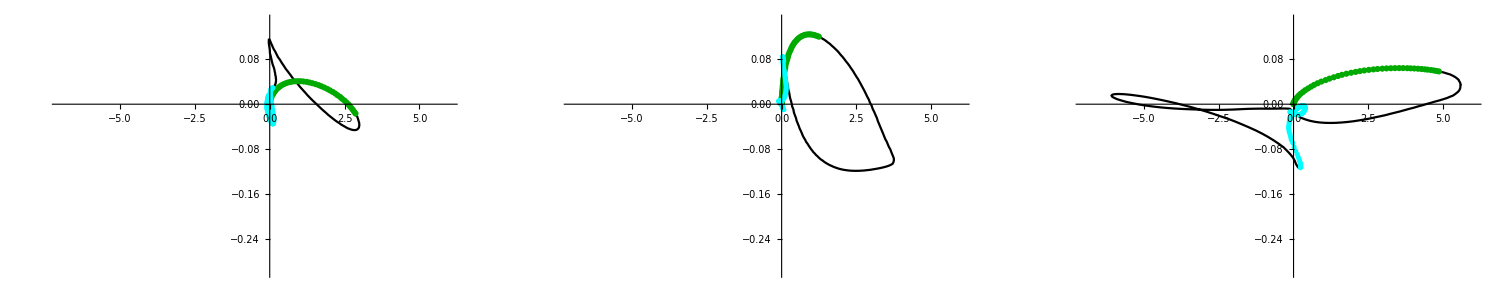

-Graphics-

```mathematica
(*open saved data from different reaches*)
SetDirectory[dirMSdata];
trialroot="A03_FB_P00_f";
reaches={"0","1","2"};(*reach trials*)
joints={"sho","elb","wri"};
trialroot="fvposDATA_A03_FB_P00_f";
reaches={"0","1","2"};(*reach trials*)
joints={"sho","elb","wri"};
suffix=".csv";
msDATAraw=Table[
trname=joints[[i]]<>trialroot<>reaches[[k]]<>suffix;
Import[trname,"Data"]
,{i,1,3},{k,1,3}];

ResetDirectory[];

shoxyrange={{-2,11},{-0.5,0.3}};
elbxyrange={{-7,6},{-0.3,0.15}};
wrixyrange={{-8,4},{-0.15,0.15}};

shofvDATAalltrials=msDATAraw[[1]];
elbfvDATAalltrials=msDATAraw[[2]];
wrifvDATAalltrials=msDATAraw[[3]];


earlyrange=Round[0.1/mjdt];
laterange=Round[0.2/mjdt];
thicknessf7=Thickness[0.004];
sizef7=1500;
colstart=Darker@Green;
colend=Cyan;
GraphicsRow[
Table[Show[
ListLinePlot[shofvDATAalltrials[[i]],PlotRange->shoxyrange,PlotStyle->{Black,thicknessf7},BaseStyle->graphstyle,AxesStyle->Thickness[axthickness]](*whole trial*),
ListPlot[shofvDATAalltrials[[i,1;;earlyrange]],PlotRange->shoxyrange,PlotStyle->colstart](*early portion*),
ListPlot[shofvDATAalltrials[[i,-laterange;;]],PlotRange->shoxyrange,PlotStyle->colend](*lateportion*)
(*,ImageSize->size*)]
,{i,1,3}]
,ImageSize->sizef7]

GraphicsRow[
Table[Show[
ListLinePlot[elbfvDATAalltrials[[i]],PlotRange->elbxyrange,PlotStyle->{Black,thicknessf7},BaseStyle->graphstyle,AxesStyle->Thickness[axthickness]](*whole trial*),
ListPlot[elbfvDATAalltrials[[i,1;;earlyrange]],PlotStyle->colstart](*early portion*),
ListPlot[elbfvDATAalltrials[[i,-laterange;;]],PlotStyle->colend](*lateportion*)
(*,ImageSize->size*)]
,{i,1,3}]
,ImageSize->sizef7]

GraphicsRow[
Table[Show[
ListLinePlot[wrifvDATAalltrials[[i]],PlotRange->wrixyrange,PlotStyle->{Black,thicknessf7},BaseStyle->graphstyle,AxesStyle->Thickness[axthickness]](*whole trial*),
ListPlot[wrifvDATAalltrials[[i,1;;earlyrange]],PlotStyle->colstart](*early portion*),
ListPlot[wrifvDATAalltrials[[i,-laterange;;]],PlotStyle->colend](*lateportion*)
(*,ImageSize->size*)]
,{i,1,3}]
,ImageSize->sizef7]
```

```mathematica
(*for the stick figures*)

SetDirectory[dirFigures];
range=1;
ptarget=ListPointPlot3D[{targetXYZ},PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1},PlotStyle->{Red,PointSize[0.04]},Axes->False,Boxed->False];
stickframes={1,100,-1};
Do[
points=Partition[xyzDATA[[stickframes[[fr]]]],3];
p2=Graphics3D[{Thickness[0.007],Line[points]}];
plot1=Show[ptarget,p2,Box->False,ViewPoint->Top,ViewAngle->0.4];
Export["stickFrames_"<>IntegerString[fr,10,2]<>"_"<>trialname<>".png",plot1]
,{fr,1,Length[stickframes]}]

ResetDirectory[];
```

```mathematica
Show[
ListLinePlot[elbfvDATAalltrials[[1]],PlotRange->elbxyrange,PlotStyle->{Black,thicknessf7},BaseStyle->graphstyle,AxesStyle->Thickness[axthickness]](*whole trial*),
ListPlot[elbfvDATAalltrials[[1,1;;earlyrange]],PlotStyle->colstart](*early portion*),
ListPlot[elbfvDATAalltrials[[1,-laterange;;]],PlotStyle->colend](*lateportion*)
,ImageSize->size,Ticks->{{-4,4},Automatic}]
```

-Graphics-

```mathematica
ptarget
```

-Graphics3D-

```mathematica
msDATAraw//Dimensions
```

## Figure 8

Step 1. Run analyseReaches for the control condition “A03_FB_P00_f0”
find the section of code that says in comments “analyse components of dtorque/dt” - set joint index to 2 (for elbow)- run that
Export the figure from this notebook
Step 2. Run analyseReaches for the perturbation condition “A03_FB _P04 _f0”
find the section of code that says in comments “analyse components of dtorque/dt” - set joint index to 2 (for elbow)- run that
Export the figure from this notebook

```mathematica
poslimit=Max[Abs@dtorqueLimitPos]
neglimit=Max[Abs@dtorqueLimitNeg]
thickness=Thickness[0.008];
dtorquerange={-1000,1000};

dactJoint=rext*fmaxExt*dadataExt-rflx*fmaxFlx*dadataFlx;
dactFlx=(*rflx*fmaxFlx**)dadataFlx;
dactExt=(*rext*fmaxExt**)dadataExt;
dactJointXY=Thread[{timeData,dactJoint}];
dactFlxXY=Thread[{timeData,(*-*)(*dactFlx*)dadataFlx}];
dactExtXY=Thread[{timeData,(*dactExt*)dadataExt}];

plot1=ListLinePlot[torqueXY,PlotRange->{Automatic,{-7,4}},ImageSize->size,PlotStyle->{Black,Thick},BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]];
plot2=ListLinePlot[{dactExtXY,dactFlxXY},PlotRange->{Automatic,dtorquerange},ImageSize->size,PlotStyle->{{Red,Thick},{Red,Thick,Dashed}},BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]];
plot3=ListLinePlot[dtorqueXY,PlotRange->{Automatic,dtorquerange},ImageSize->size,PlotStyle->{{Black,Thick},{Red,Thick},{Red,Thick,Dashed}},BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]];
plot4=Show[
p1=ListLinePlot[{(*dtorqueXY,dtorqueCalXY,*)dtorqueCalNoACTXY(*dtorqueCalNoFVGXY*)(*,dtorqueCalNoACTXY*)},PlotStyle->{{Blue,thickness},Transparent,{Cyan,Thick},{Blue,Dashed}},PlotRange->{Automatic,dtorquerange},PlotStyle->styles3,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]],
p1a=ListLinePlot[{{0,poslimit},{cutoff,dtorqueLimitPos[[1]]}},PlotStyle->{Black,Dashed}],
p1b=ListLinePlot[{{0,Sign[dtorqueLimitNeg[[1]]]*neglimit},{cutoff,dtorqueLimitPos[[2]]}},PlotStyle->{Black,Dashed}]
];

plot5=ListLinePlot[{dactFlxXY,dactExtXY},PlotRange->{Automatic,{-2,3}},ImageSize->size,PlotStyle->{{Black,Thick},{Black,Thick,Dashed}},BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]];

g=GraphicsColumn[{plot1,plot3,(*plot4,*)(*plot2*)plot5},ImageSize->500]
```

493.558

760.468

-Graphics-

```mathematica
plot5
plot3
```

-Graphics-

```mathematica
SetDirectory[dirFigures];
Export["C:\\Users\\ctrichards\\Desktop\\"<>"perturbB.png"(*"controlA.png"*),g]
ResetDirectory[];
```

SetDirectory::cdir: Cannot set current directory to /Users/chris/Desktop/WTageing/papers/ReachingLimits.

C:\Users\ctrichards\Desktop\perturbB.png

ResetDirectory::dtop: Directory stack is empty.

```mathematica
aElb
```

1.3

```mathematica
ListPlot[dadataExt-aElb*dadataFlx]
```

-Graphics-

## Figure 9

load condition A03_FB _P04 _f0 in analyseReaches.nb

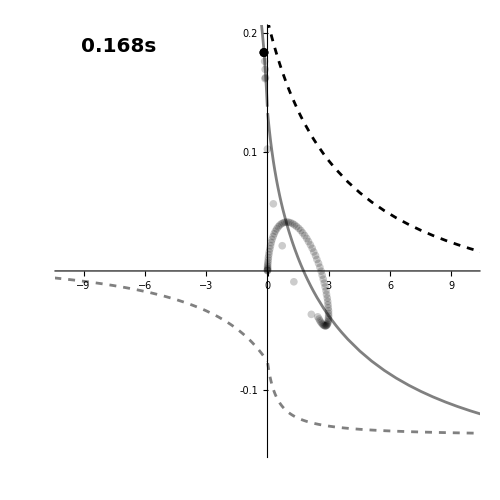

```mathematica
fr=84;(*just after perturbation*)
joint=2;(*elbow joint*)
time=ToString[NumberForm[fr*mjdt,{3,3}]]<>"s";
labelnormal=Style[time,Black,Bold,20];
labelperturb=Style[time,Red,Bold,20];
label=If[pertStart<=fr*mjdt<=pertEnd,labelperturb,labelnormal];
points=Partition[xyzDATA[[fr]],3];
DATA={shofvDATA2D,elbfvDATA2D,wrifvDATA2D}[[joint]];
p2=Graphics3D[{Thickness[0.007],Line[points]}];
plot2=Show[
DATA[[fr]],
PlotRange->(*{All,{-yrange,yrange}}*){{-10,10},{-0.15,0.2}},PlotStyle->Thick,BaseStyle->graphstyle,AxesStyle->Thickness[2*axthickness]];
(*GraphicsRow[{plot1,plot2},ImageSize->800]*)
frame=Show[plot2,Epilog->Inset[label,Scaled[{0.15,.95}]],ImageSize->500,Ticks->{Automatic,{-0.1,0.1,0.2}}]
```

```mathematica
figurePlot=GraphicsColumn[{pqvel,pqacc,ptrq},ImageSize->500,ImagePadding->{{0,Automatic},None}]
```

-Graphics-

```mathematica
SetDirectory[dirFigures]
Export["timeSeriesData_torqueandAccel.png",figurePlot]
```

/Users/chris/Desktop/WTageing/papers/ReachingLimits

timeSeriesData_torqueandAccel.png

## SI movies

movie 3 control reach 1: forward reach (technical name A03_FB_P00_f0)
movie 4 control reach 2: sideways reach (technical name A03_FB_P00_f1)
movie 5 control reach 3: cross-body reach (technical name A03_FB_P00_f2)

movie 6 perturbed reach 1: forward reach (technical name A03_FB_P04_f0)


Directions - run analyseReaches.nb using technical name as the trial name;  run the joint FV volume section

```mathematica
yrange=(*0.05*)(*0.75*)0.5;
pertTimings={
{"A03_FB_P01_f0",0.022},{"A03_FB_P02_f0",0.064},{"A03_FB_P03_f0",0.106},{"A03_FB_P04_f0",0.148},
{"A03_FB_P01_f1",0.032},{"A03_FB_P02_f1",0.094},{"A03_FB_P03_f1",0.158},{"A03_FB_P04_f1",0.222},
{"A03_FB_P01_f2",0.038},{"A03_FB_P02_f2",0.116},{"A03_FB_P03_f2",0.192},{"A03_FB_P04_f2",0.270}
};
(*perturbation never happens for controls, so make start time arbitrarily large*)
pertTimingsControl={{"A03_FB_P00_f0",10},{"A03_FB_P00_f1",10},{"A03_FB_P00_f2",10}};
pertTimings=Join[pertTimings,pertTimingsControl];
pertStart=pertTimings[[Position[pertTimings,trialname][[1,1]]]][[2]];
pertEnd=pertStart+0.018;

isPerturb=ToExpression@StringPart[trialname,10]!=0;(*determine if a perturbed trial*)
pertColor=If[isPerturb,Red,Black];
framePanels={};
ptarget=ListPointPlot3D[{targetXYZ},PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1},PlotStyle->Red,Axes->False,Boxed->False];

(*for stick figure inset*)
framePanelsStick=Table[
fr=i;
time=ToString[NumberForm[fr*mjdt,{3,3}]]<>"s";
labelnormal=Style[time,Black,Bold,20];
labelperturb=Style[time,Red,Bold,20];
label=If[pertStart<=fr*mjdt<=pertEnd,labelperturb,labelnormal];
points=Partition[xyzDATA[[fr]],3];
DATA={shofvDATA2D,elbfvDATA2D,wrifvDATA2D}[[1]];
p2=Graphics3D[{Thickness[0.007],Line[points]}];
plot1=Show[ptarget,p2,Box->False,ViewPoint->Top,ViewAngle->0.4];
plot2=Show[
DATA[[fr]],
PlotRange->{All,{-yrange,yrange}},PlotStyle->Thick,PlotLabel->label];
(*GraphicsRow[{plot1,plot2},ImageSize->800]*)
frame=Show[plot1,ImageSize->500]

,{i,1,Length[actDATA]}];
```

```mathematica
(*for FV trajectories*)
framePanels=Table[
fr=i;
time=ToString[NumberForm[fr*mjdt,{3,3}]]<>"s";

(*time and joint labels*)
sholabelnormal=Style["Shoulder "<>time,Black,Bold,20];
sholabelperturb=Style["Shoulder "<>time,pertColor,Bold,20];
sholabel=If[pertStart<=fr*mjdt<=pertEnd,sholabelperturb,sholabelnormal];

elblabelnormal=Style["Elbow "<>time,Black,Bold,20];
elblabelperturb=Style["Elbow "<>time,pertColor,Bold,20];
elblabel=If[pertStart<=fr*mjdt<=pertEnd,elblabelperturb,elblabelnormal];

wrilabelnormal=Style["Wrist "<>time,Black,Bold,20];
wrilabelperturb=Style["Wrist "<>time,pertColor,Bold,20];
wrilabel=If[pertStart<=fr*mjdt<=pertEnd,wrilabelperturb,wrilabelnormal];

points=Partition[xyzDATA[[fr]],3];
p2=Graphics3D[{Thickness[0.007],Line[points]}];
plot1=Show[ptarget,p2,Box->False,ViewPoint->Top,ViewAngle->0.4];
plotSho=Show[
shofvDATA2D[[fr]],
PlotRange->{All,{-yrange,yrange}},PlotStyle->Thick,PlotLabel->sholabel,BaseStyle->graphstyle,AxesStyle->Thickness[axthickness]];

plotElb=Show[
elbfvDATA2D[[fr]],
PlotRange->{All,{-yrange,yrange}},PlotStyle->Thick,PlotLabel->elblabel,BaseStyle->graphstyle,AxesStyle->Thickness[axthickness]];

plotWri=Show[
wrifvDATA2D[[fr]],
PlotRange->{All,{-yrange,yrange}},PlotStyle->Thick,PlotLabel->wrilabel,BaseStyle->graphstyle,AxesStyle->Thickness[axthickness]];

frameSho=Show[plotSho,ImageSize->500,Epilog->{Inset[framePanelsStick[[fr]],{1,.25},{0,0.5},Scaled[.5]]}];
frameElb=Show[plotElb,ImageSize->500];
frameWri=Show[plotWri,ImageSize->500];

frame=GraphicsRow[{frameSho,frameElb,frameWri},ImageSize->1500]

,{i,1,Length[actDATA]}];

Beep[]
```

```mathematica
SetDirectory[dirFigures];
(*Export["SI_movie_03_control_forward_reach.mov",framePanels]*)
(*Export["SI_movie_04_control_sideways_reach.mov",framePanels]*)
(*Export["SI_movie_05_control_crossbody_reach.mov",framePanels]*)
Export["SI_movie_06_perturbed_forward_reach.mov",framePanels]
Beep[]
ResetDirectory[];
```

## Figure 3 EGG

This is a toy model of an arbitrary single joint (elbow joint) with lumped mass = mass of the entire arm.  The joint is actuated by two identical antagonistic muscles with identical moment arms and lumped parameters from [1].  Simple PD feedback to make the arm follow a bell-shaped velocity trajectory (as used in [1]).  Force-length properties are not present.  

[1] Murtola & Richards 2023 doi:10.1080/10255842.2022.2089022

```mathematica
(*---------1.  Define FV and activation functions for the muscles----------*)

(*This is the shortening and lengthening portions of the FV curve *)
(*as they appear in Murtola & Richards 2023 *)
FVpiecewise[vmreal_,vmax_,d1_,d2_,d3_,offset_:0]:=Module[{fvshort,fvlength,vm},
vm=(vmreal+offset);
fvshort=(1-vm/vmax)/(1+d1*vm/vmax);(*shortening portion*)
fvlength=d2-((d2-1)*(1+vm/vmax))/(1-d3*vm/vmax);
Piecewise[{{fvshort,vm>=0},{fvlength,vm<0}}]
]


fvparam={4,1.8,30.24};(*d1, d2, d3 parameters for the fv curve*)
(*rValues={0.045,0.045,0.041,0.041,0.035,0.035};(*moment arm values for the reaching model - not used here*)
optLengths={0.266872,0.298288,0.316149,0.440375,0.293339,0.317774};(*optimal length values used for reaching model*)*)
vmax=1.6;(*the maximum shortening velocity value in ML/s used for original reaching study*)

FV=FVpiecewise[vm,vmax,fvparam[[1]],fvparam[[2]],fvparam[[3]]];(*FV function specific for the above parameters*)
FVfun1=FV;(*FV fun for muscle 1, agonist*)
FVfun2=FV/.vm->-vm;(*FV fun for muscle 2, antagonist*)


parametersAO3={0.018,0.040,0.025,0.6,0.8,0.7};(*3rd order muscle activation function converts excitation --> activation as in [1]*)
(*identical to the above, but accepts 2 parameters  for 1st order activation*)
actModel[parameters_,excitationFunction_,tfinal_]:=Module[{ao3Q,sixParameters,t1,t2,t3,b1,b2,b3,fdm1,fdm2,fdm3,actdata,a1,a2,a3,npoints,tf,output},
ao3Q=Length[parameters]==6;
sixParameters=If[ao3Q,parameters,Join[parameters,{1,1,1,1}](*dummy parameters which aren't used*)];
tf=tfinal;
t1=sixParameters[[1]];t2=sixParameters[[2]];t3=sixParameters[[3]];b1=sixParameters[[4]];b2=sixParameters[[5]];b3=sixParameters[[6]];
fdm1=NDSolve[{a1'[t]+a1[t]((1/t1)*(b1+(1-b1)*excitationFunction))==(1/t1)*excitationFunction,a1[0]==0},{a1[t]},{t,0,tf}, MaxStepSize->1];
fdm2=NDSolve[{a2'[t]+a2[t]((1/t2)*(b2+(1-b2)*a1[t]/.fdm1[[1]]))==(1/t2)*a1[t]/.fdm1[[1]],a2[0]==0},{a2[t]},{t,0,tf}, MaxStepSize->1];
fdm3=NDSolve[{a3'[t]+a3[t]((1/t3)*(b3+(1-b3)*a2[t]/.fdm2[[1]]))==(1/t3)*a2[t]/.fdm2[[1]],a3[0]==0},{a3[t]},{t,0,tf}, MaxStepSize->1];
output=If[ao3Q,a3[t]/.fdm3[[1]],a1[t]/.fdm1[[1]]]
]


(*---------2.  Define the toy arm/joint properties----------*)
mforearm=1.1;mhand=0.41;
lforearm=0.25;lhand=0.18;
mass=mforearm+mhand;(*arm mass lumped from forearm + hand*)
lo=lforearm+lhand;(*set muscle length = length of lower arm + hand*)
rmass=(mforearm*lforearm+mhand*lhand)/mass;(*centre of mass used for calculating moment of inertia*)
moi=mass*rmass^2;(*arm moment of inertia*)
r=0.3*lo/(Pi/2);(*moment arm = necessary length for muscle to shorten 30% for a 90 degree movement*)
fmax=1300;(*lumped max isometric force for elbow muscles, based on [1]]*)

(*---------3.  Define the bell-shaped velocity trajectory that the joint must follow----------*)
dur=2.5;(*duration of simulation*)
durTraj=2.0;(*duration of trajectory*)
factor=0.67;(*iadjust desired velocity so joint reaches ~90 degrees*)
bellfunRaw=factor*(1/durTraj)*(30(t/durTraj)^4-60(t/durTraj)^3+30(t/durTraj)^2);(*same function used in [1] for joint velocity in rad/s*)
bellfun=Piecewise[{{bellfunRaw,t<=durTraj},{0,t>durTraj}}];
(*vel=bellfun/lo;(*muscle velocity in muscle lengths/s*)*)
(*vel=r*bellfun/lo;(*muscle velocity in muscle lengths/s*)*)
vel=bellfun;(*joint angular velocity in rad/s*)
acc=D[bellfun,t];(*joint acceleration*)
(*frc=mass*acc;(*muscle force*)*)
trq=moi*acc;(*joint torque*)
velplot=Plot[vel,{t,0,dur}];
trqplot=Plot[trq,{t,0,dur}];
(*plot torque vs velocity*)
fvplot=ParametricPlot[{vel,trq},{t,0,dur},AspectRatio->1];
```

{{x[t]→InterpolatingFunction[…][t],x'[t]→InterpolatingFunction[…][t],x''[t]→InterpolatingFunction[…][t]}}

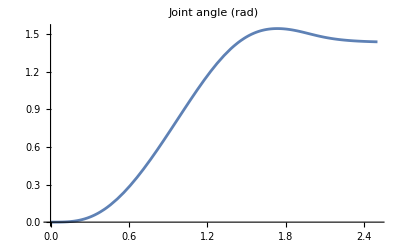

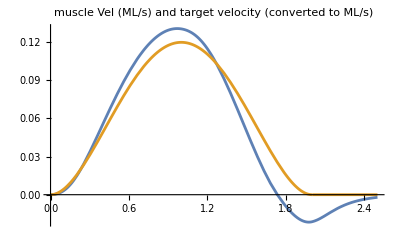

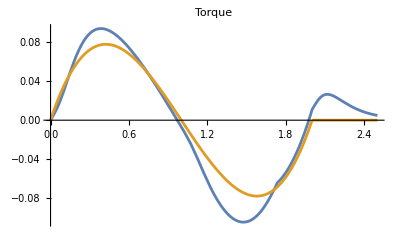

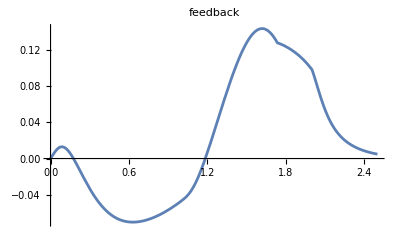

ListPlot::lpn: fvDataSim is not a list of numbers or pairs of numbers.

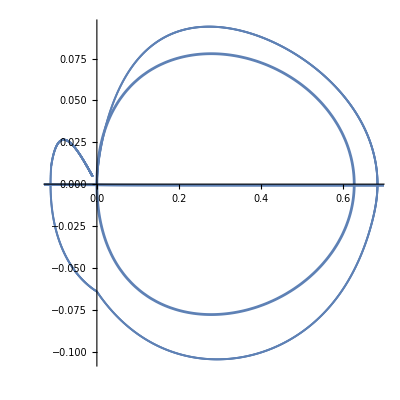

```mathematica
(*----------4.  Define arbitrary feed forward muscle activations for antagonist muscles (i.e. muscles 1, 2)--------*)
(*excitation is arbitrary based on expected force profile - it will be corrected with feedback anyway*)
(*activation will be computed with 3rd order activation dynamics as in [1]*)

factor1=factor2=0.008;(*arbitrary factor to scale magnitude of activations - as necessary*)
exc1=factor1*Clip[trq,{0,100}];(*positive portion of force curve turned into an excitation function*)
exc2=-factor2*Clip[trq,{-100,0}];(*negative portion of force curve turned into an excitation function*)
act1=actModel[parametersAO3,exc1,dur];
act2=actModel[parametersAO3,exc2,dur];
(*to make code run faster, make activation and FV functions into interpolating functions*)
act1i=Interpolation[Table[{t,act1},{t,0,dur,0.001}]];
act2i=Interpolation[Table[{t,act2},{t,0,dur,0.001}]];
FVfun1i=Interpolation[Table[{vm,FVfun1},{vm,-vmax,vmax,0.001}]];
FVfun2i=Interpolation[Table[{vm,FVfun2},{vm,-vmax,vmax,0.001}]];

(*----------5.  Use forward dynamics to solve motion tracking with feedback given feedforward excitations--------*)

gfb=0.1;gp=10;gd=1;(*feedback gains - overall gain, proportional gain, derivative gain*)
gmus=1(*muscle gain*);
v0=0;(*initial velocity*)
err=vel-x'[t];(*error with respect to target velocity trajectory*)
(*fb=gfb*(gp*err+gd*D[err,t])(*total feedback signal - unused*);*)
fbRaw=gfb*(gp*err+gd*D[err,t]);(*raw feedback signam*)
fb=fbRaw;
fbExc1=factor1*Clip[fbRaw,{0,100}];(*feedback excitation to agonist*)
fbExc2=-factor2*Clip[fbRaw,{-100,0}];(*feedback excitation to antagonist*)
velMus=r*x'[t]/lo;(*muscle velocity in muscle lengths/s*)
(*trqNet=(gmus*fmax*r*((act1i[t]+fbExc1)*FVfun1i[velMus]-(act2i[t]+fbExc2)*FVfun2i[velMus])(*+fb*));*)
trqNet=(gmus*fmax*r*(act1i[t]*FVfun1i[velMus]-act2i[t]*FVfun2i[velMus])+fb);
(*net torque on mass as a function of time-varying activation and FV curve*)

(*---joint force-velocity curves---*)
jointfv=act1*FVfun1-act2*FVfun2;
jointfv1=act1*FVfun1;
jointfv2=-act2*FVfun2;

(*---numerically solve dynamics equations-----*)
(*NDSolve command is the numerical integrator used to solve the ODE where x is the joint angle*)
fdm=NDSolve[
{x''[t]==(trqNet/moi),x'[0]==v0,x[0]==0},{x[t],x'[t],x''[t]},{t,0,dur}
,InterpolationOrder->5]
Plot[x[t]/lo(*frcFL*)/.fdm,{t,0,dur},PlotLabel->"Joint angle (rad)"]
Plot[{velMus/.fdm,r*vel/lo},{t,0,dur},PlotLabel->"muscle Vel (ML/s) \nand target velocity (converted to ML/s)"]
Plot[{trqNet/.fdm,trq},{t,0,dur},PlotLabel->"Torque",PlotStyle->styles,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]]
Plot[fb/.fdm,{t,0,dur},PlotRange->All,PlotLabel->"feedback"]
fvsimPlot=ListPlot[fvDataSim];
fvDataSim=Table[{x'[t],trqNet}/.fdm[[1]],{t,0,dur,0.001}];
jointfvCurvePlot=Plot[jointfv/.fdm[[1]]/.t->1.2,{vm,-vmax,vmax}];
Show[fvsimPlot,fvplot,jointfvCurvePlot,AspectRatio->1]
```

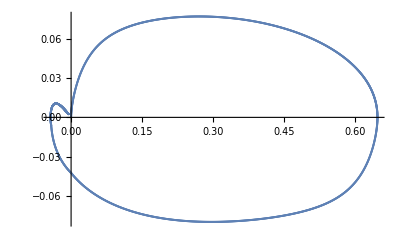

```mathematica
fvsimPlot
```

```mathematica
jointfv=act1*FVfun1-act2*FVfun2;
jointfv1=act1*FVfun1;
jointfv2=-act2*FVfun2;
```

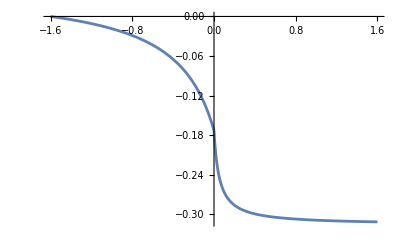

```mathematica
Plot[jointfv/.fdm[[1]]/.t->1.5,{vm,-vmax,vmax}]
```

```mathematica
jointfv
```

-(Piecewise[{{(1+0.625 vm)/(1-2.5 vm), -vm≥0}, {1.8-(0.8 (1-0.625 vm))/(1+18.9 vm), -vm<0}, {0, True}}]) InterpolatingFunction[…][t]+(Piecewise[{{(1-0.625 vm)/(1+2.5 vm), vm≥0}, {1.8-(0.8 (1+0.625 vm))/(1-18.9 vm), vm<0}, {0, True}}]) InterpolatingFunction[…][t]